```mathematica
Clear["Global`*"]
Needs["ErrorBarLogPlots`"]

Rad1={{{-150.,0.},ErrorBar[{0.,0.017857142857142856}]},{{-147.,0.031746031746031744},ErrorBar[{-0.015787977512734478,0.030420914020670986}]},{{-144.,0.015384615384615385},ErrorBar[{-0.009492683239570322,0.02417799792488501}]},{{-141.,0.},ErrorBar[{0.,0.015625}]},{{-138.,0.017543859649122806},ErrorBar[{-0.010822487442062156,0.02745890607485102}]},{{-135.,0.06060606060606061},ErrorBar[{-0.02332088215069532,0.03643711914752931}]},{{-132.,0.015151515151515152},ErrorBar[{-0.00934908778680136,0.023822176886756127}]},{{-129.,0.06349206349206349},ErrorBar[{-0.024414058653599753,0.03805493166947277}]},{{-126.,0.031746031746031744},ErrorBar[{-0.015787977512734478,0.030420914020670986}]},{{-123.,0.046153846153846156},ErrorBar[{-0.019850139270147144,0.033603053023060894}]},{{-120.,0.08928571428571429},ErrorBar[{-0.031245453615454284,0.045656481184376554}]},{{-117.,0.19607843137254902},ErrorBar[{-0.04952265838885245,0.06121194948990824}]},{{-114.,0.46551724137931033},ErrorBar[{-0.0643576449158611,0.06552655198774898}]},{{-111.,0.49206349206349204},ErrorBar[{-0.06236824108683914,0.06261625695985512}]},{{-108.,0.3055555555555556},ErrorBar[{-0.05131624239362359,0.05664348744689596}]},{{-105.,0.058823529411764705},ErrorBar[{-0.022644878653454555,0.0354326024386208}]},{{-102.,0.078125},ErrorBar[{-0.02742344632413153,0.04040421555490076}]},{{-99.,0.05357142857142857},ErrorBar[{-0.02300364611369494,0.03866780651469744}]},{{-96.,0.06153846153846154},ErrorBar[{-0.023674238923818244,0.03696095221053153}]},{{-93.,0.03389830508474576},ErrorBar[{-0.01685210974350771,0.0323888329073495}]},{{-90.,0.015151515151515152},ErrorBar[{-0.00934908778680136,0.023822176886756127}]},{{-87.,0.},ErrorBar[{0.,0.01639344262295082}]},{{-84.,0.},ErrorBar[{0.,0.015384615384615385}]},{{-81.,0.01694915254237288},ErrorBar[{-0.010456289660084668,0.02655798457533891}]},{{-78.,0.015384615384615385},ErrorBar[{-0.009492683239570322,0.02417799792488501}]},{{-75.,0.03278688524590164},ErrorBar[{-0.016302699058847674,0.03137408985736697}]},{{-72.,0.04477611940298507},ErrorBar[{-0.01926327415128954,0.03265221181590763}]},{{-69.,0.},ErrorBar[{0.,0.015151515151515152}]},{{-66.,0.016129032258064516},ErrorBar[{-0.009951213952763435,0.025312197055682016}]},{{-63.,0.015625},ErrorBar[{-0.00964075849483767,0.024544604648683827}]},{{-60.,0.},ErrorBar[{0.,0.015384615384615385}]},{{-57.,0.014925373134328358},ErrorBar[{-0.009209771873323409,0.023476672663490225}]},{{-54.,0.028985507246376812},ErrorBar[{-0.014421939112947594,0.0278794960487654}]},{{-51.,0.014705882352941176},ErrorBar[{-0.009074546997179186,0.023141043160862056}]},{{-48.,0.},ErrorBar[{0.,0.015384615384615385}]},{{-45.,0.014285714285714285},ErrorBar[{-0.008815670122704669,0.022497762678036666}]},{{-42.,0.},ErrorBar[{0.,0.015384615384615385}]},{{-39.,0.03076923076923077},ErrorBar[{-0.015304760608483632,0.029523874827597857}]},{{-36.,0.},ErrorBar[{0.,0.014925373134328358}]},{{-33.,0.},ErrorBar[{0.,0.01694915254237288}]},{{-30.,0.},ErrorBar[{0.,0.014705882352941176}]},{{-27.,0.05172413793103448},ErrorBar[{-0.022219260068879813,0.03741505200342104}]},{{-24.,0.06060606060606061},ErrorBar[{-0.02332088215069532,0.03643711914752931}]},{{-21.,0.06557377049180328},ErrorBar[{-0.02520157474752588,0.039215324086499956}]},{{-18.,0.07017543859649122},ErrorBar[{-0.02693940026061558,0.041760936860736564}]},{{-15.,0.03389830508474576},ErrorBar[{-0.01685210974350771,0.0323888329073495}]},{{-12.,0.029411764705882353},ErrorBar[{-0.014632957429090569,0.028273196133267904}]},{{-9.,0.05172413793103448},ErrorBar[{-0.022219260068879813,0.03741505200342104}]},{{-6.,0.12121212121212122},ErrorBar[{-0.03461814609739462,0.04592524695673425}]},{{-3.,0.1774193548387097},ErrorBar[{-0.043281667204219526,0.05352232260616521}]},{{0.,0.4262295081967213},ErrorBar[{-0.061626538382920704,0.06400623166689745}]},{{3.,0.3333333333333333},ErrorBar[{-0.06224544184827607,0.06865569825853252}]},{{6.,0.296875},ErrorBar[{-0.05363020985912961,0.059880209859129674}]},{{9.,0.17543859649122806},ErrorBar[{-0.04465797000138927,0.0558497425361745}]},{{12.,0.08064516129032258},ErrorBar[{-0.02828863829201838,0.04160149031454782}]},{{15.,0.07272727272727272},ErrorBar[{-0.027901316359720534,0.04316105661946079}]},{{18.,0.03278688524590164},ErrorBar[{-0.016302699058847674,0.03137408985736697}]},{{21.,0.03333333333333333},ErrorBar[{-0.016572852742406014,0.031873399190493444}]},{{24.,0.},ErrorBar[{0.,0.013513513513513514}]},{{27.,0.},ErrorBar[{0.,0.015625}]},{{30.,0.01694915254237288},ErrorBar[{-0.010456289660084668,0.02655798457533891}]},{{33.,0.},ErrorBar[{0.,0.019230769230769232}]},{{36.,0.},ErrorBar[{0.,0.015151515151515152}]},{{39.,0.},ErrorBar[{0.,0.015151515151515152}]},{{42.,0.},ErrorBar[{0.,0.015625}]},{{45.,0.037037037037037035},ErrorBar[{-0.018402528041788054,0.03523754487680489}]},{{48.,0.01694915254237288},ErrorBar[{-0.010456289660084668,0.02655798457533891}]},{{51.,0.},ErrorBar[{0.,0.017857142857142856}]},{{54.,0.},ErrorBar[{0.,0.01639344262295082}]},{{57.,0.},ErrorBar[{0.,0.018518518518518517}]},{{60.,0.},ErrorBar[{0.,0.01639344262295082}]},{{63.,0.015873015873015872},ErrorBar[{-0.009793526508861415,0.02492249476282967}]},{{66.,0.014705882352941176},ErrorBar[{-0.009074546997179186,0.023141043160862056}]},{{69.,0.},ErrorBar[{0.,0.014705882352941176}]},{{72.,0.014925373134328358},ErrorBar[{-0.009209771873323409,0.023476672663490225}]},{{75.,0.},ErrorBar[{0.,0.017857142857142856}]},{{78.,0.016129032258064516},ErrorBar[{-0.009951213952763435,0.025312197055682016}]},{{81.,0.03333333333333333},ErrorBar[{-0.016572852742406014,0.031873399190493444}]},{{84.,0.034482758620689655},ErrorBar[{-0.017140938019669972,0.03292118349015509}]},{{87.,0.029850746268656716},ErrorBar[{-0.014850242027236758,0.028678161254629204}]},{{90.,0.015151515151515152},ErrorBar[{-0.00934908778680136,0.023822176886756127}]},{{93.,0.015625},ErrorBar[{-0.00964075849483767,0.024544604648683827}]},{{96.,0.10144927536231885},ErrorBar[{-0.03083947585912293,0.04222663942019955}]},{{99.,0.16901408450704225},ErrorBar[{-0.03980797105078443,0.04900202425892214}]},{{102.,0.24242424242424243},ErrorBar[{-0.048652203514020415,0.05634103209837138}]},{{105.,0.36231884057971014},ErrorBar[{-0.05551786958582944,0.05945161699783774}]},{{108.,0.3333333333333333},ErrorBar[{-0.057686733299169346,0.06315121417348629}]},{{111.,0.23809523809523808},ErrorBar[{-0.049304495746602756,0.057489019556126564}]},{{114.,0.10344827586206896},ErrorBar[{-0.03349262792290725,0.04693505924961679}]},{{117.,0.014925373134328358},ErrorBar[{-0.009209771873323409,0.023476672663490225}]},{{120.,0.03278688524590164},ErrorBar[{-0.016302699058847674,0.03137408985736697}]},{{123.,0.08333333333333333},ErrorBar[{-0.02921012556905169,0.04287132775484402}]},{{126.,0.058823529411764705},ErrorBar[{-0.022644878653454555,0.0354326024386208}]},{{129.,0.},ErrorBar[{0.,0.015873015873015872}]},{{132.,0.015625},ErrorBar[{-0.00964075849483767,0.024544604648683827}]},{{135.,0.},ErrorBar[{0.,0.015384615384615385}]},{{138.,0.015151515151515152},ErrorBar[{-0.00934908778680136,0.023822176886756127}]},{{141.,0.},ErrorBar[{0.,0.015625}]},{{144.,0.03076923076923077},ErrorBar[{-0.015304760608483632,0.029523874827597857}]},{{147.,0.0196078431372549},ErrorBar[{-0.012093043801077799,0.03056966521887569}]},{{150.,0.},ErrorBar[{0.,0.01694915254237288}]}};
Rad2={{{-160.,0.02857142857142857},ErrorBar[{-0.012334107121829817,0.02122898582802928}]},{{-157.,0.02912621359223301},ErrorBar[{-0.012572137106696864,0.021627402229923154}]},{{-154.,0.009900990099009901},ErrorBar[{-0.006112728613093586,0.015722513120956134}]},{{-151.,0.},ErrorBar[{0.,0.009345794392523364}]},{{-148.,0.},ErrorBar[{0.,0.009615384615384616}]},{{-145.,0.019417475728155338},ErrorBar[{-0.009677078337118674,0.018919049957731075}]},{{-142.,0.019230769230769232},ErrorBar[{-0.009584333281451434,0.0187418424389606}]},{{-139.,0.02247191011235955},ErrorBar[{-0.011193500746643738,0.0218052360774802}]},{{-136.,0.09574468085106383},ErrorBar[{-0.026231584396585697,0.03474222269445801}]},{{-133.,0.32323232323232326},ErrorBar[{-0.04503677350851565,0.048572127043869096}]},{{-130.,0.57},ErrorBar[{-0.04995982298861279,0.0485736843747514}]},{{-127.,0.35789473684210527},ErrorBar[{-0.04746873744566932,0.05042926376145884}]},{{-124.,0.15384615384615385},ErrorBar[{-0.03206788503395547,0.03866129162736204}]},{{-121.,0.056074766355140186},ErrorBar[{-0.018406057765267284,0.026626895425357282}]},{{-118.,0.034482758620689655},ErrorBar[{-0.014867443021315957,0.025447380325391192}]},{{-115.,0.0297029702970297},ErrorBar[{-0.01281953406359818,0.022041044449930942}]},{{-112.,0.08737864077669903},ErrorBar[{-0.024005807762148126,0.03194083390105776}]},{{-109.,0.14018691588785046},ErrorBar[{-0.03024160355114705,0.03690480881248315}]},{{-106.,0.07920792079207921},ErrorBar[{-0.02293116706459486,0.031181992147103127}]},{{-103.,0.02830188679245283},ErrorBar[{-0.012218440076490915,0.021035227239248798}]},{{-100.,0.01818181818181818},ErrorBar[{-0.00906316424926649,0.017744572930675176}]},{{-97.,0.009345794392523364},ErrorBar[{-0.005770299770499095,0.014856488763230142}]},{{-94.,0.01098901098901099},ErrorBar[{-0.006783670825304525,0.017414344499456454}]},{{-91.,0.009345794392523364},ErrorBar[{-0.005770299770499095,0.014856488763230142}]},{{-88.,0.009433962264150943},ErrorBar[{-0.005824681909143419,0.01499414055841163}]},{{-85.,0.01020408163265306},ErrorBar[{-0.006299649647169579,0.01619451668489376}]},{{-82.,0.010101010101010102},ErrorBar[{-0.006236085268690784,0.01603406506667058}]},{{-79.,0.},ErrorBar[{0.,0.009615384615384616}]},{{-76.,0.01},ErrorBar[{-0.006173790817485192,0.015876761114514894}]},{{-73.,0.009433962264150943},ErrorBar[{-0.005824681909143419,0.01499414055841163}]},{{-70.,0.},ErrorBar[{0.,0.010101010101010102}]},{{-67.,0.},ErrorBar[{0.,0.010526315789473684}]},{{-64.,0.018867924528301886},ErrorBar[{-0.009404075894267935,0.018397198800280994}]},{{-61.,0.010869565217391304},ErrorBar[{-0.006710020677411977,0.0172289547587584}]},{{-58.,0.010416666666666666},ErrorBar[{-0.0064307467490441455,0.016525248467257204}]},{{-55.,0.030612244897959183},ErrorBar[{-0.013209438699726468,0.022692019610878807}]},{{-52.,0.},ErrorBar[{0.,0.009708737864077669}]},{{-49.,0.},ErrorBar[{0.,0.010752688172043012}]},{{-46.,0.01},ErrorBar[{-0.006173790817485192,0.015876761114514894}]},{{-43.,0.},ErrorBar[{0.,0.009900990099009901}]},{{-40.,0.018691588785046728},ErrorBar[{-0.009316466071863608,0.018229584798066443}]},{{-37.,0.},ErrorBar[{0.,0.010309278350515464}]},{{-34.,0.01020408163265306},ErrorBar[{-0.006299649647169579,0.01619451668489376}]},{{-31.,0.009708737864077669},ErrorBar[{-0.0059941575318364325,0.015422835649834942}]},{{-28.,0.},ErrorBar[{0.,0.010752688172043012}]},{{-25.,0.01020408163265306},ErrorBar[{-0.006299649647169579,0.01619451668489376}]},{{-22.,0.02857142857142857},ErrorBar[{-0.012334107121829817,0.02122898582802928}]},{{-19.,0.04716981132075472},ErrorBar[{-0.01669532523614024,0.025159440912387823}]},{{-16.,0.043859649122807015},ErrorBar[{-0.015537236880650722,0.023470112548080166}]},{{-13.,0.0297029702970297},ErrorBar[{-0.01281953406359818,0.022041044449930942}]},{{-10.,0.},ErrorBar[{0.,0.009523809523809525}]},{{-7.,0.},ErrorBar[{0.,0.010752688172043012}]},{{-4.,0.02},ErrorBar[{-0.009966404700315352,0.019471355195364862}]},{{-1.,0.13043478260869565},ErrorBar[{-0.031174122103540786,0.03912176118722474}]},{{2.,0.2755102040816326},ErrorBar[{-0.042691821978646766,0.047226969370937066}]},{{5.,0.46078431372549017},ErrorBar[{-0.04873544019408094,0.04949690983047922}]},{{8.,0.29411764705882354},ErrorBar[{-0.04294166236571367,0.04693937795680442}]},{{11.,0.14942528735632185},ErrorBar[{-0.03422822329631689,0.04219583040185501}]},{{14.,0.061946902654867256},ErrorBar[{-0.019059343019124486,0.026744485077811034}]},{{17.,0.09803921568627451},ErrorBar[{-0.02565672120316903,0.03346178497625109}]},{{20.,0.09574468085106383},ErrorBar[{-0.026231584396585697,0.03474222269445801}]},{{23.,0.06306306306306306},ErrorBar[{-0.019396290516131662,0.027198735818576986}]},{{26.,0.030612244897959183},ErrorBar[{-0.013209438699726468,0.022692019610878807}]},{{29.,0.008928571428571428},ErrorBar[{-0.005512941820785222,0.014204471530014046}]},{{32.,0.010416666666666666},ErrorBar[{-0.0064307467490441455,0.016525248467257204}]},{{35.,0.010309278350515464},ErrorBar[{-0.0063645231854834484,0.016358211382411704}]},{{38.,0.00980392156862745},ErrorBar[{-0.006052862451156915,0.015571232906135025}]},{{41.,0.009708737864077669},ErrorBar[{-0.0059941575318364325,0.015422835649834942}]},{{44.,0.009523809523809525},ErrorBar[{-0.005880098843413838,0.015134366588247617}]},{{47.,0.01020408163265306},ErrorBar[{-0.006299649647169579,0.01619451668489376}]},{{50.,0.0196078431372549},ErrorBar[{-0.00977163580311849,0.019099638848997035}]},{{53.,0.02},ErrorBar[{-0.009966404700315352,0.019471355195364862}]},{{56.,0.009615384615384616},ErrorBar[{-0.005936580392359165,0.015277239733018508}]},{{59.,0.0196078431372549},ErrorBar[{-0.00977163580311849,0.019099638848997035}]},{{62.,0.02040816326530612},ErrorBar[{-0.010169095477921426,0.019857819452359694}]},{{65.,0.01904761904761905},ErrorBar[{-0.009493349024110692,0.018567922249627306}]},{{68.,0.021505376344086023},ErrorBar[{-0.010713822130281249,0.02089455880381133}]},{{71.,0.},ErrorBar[{0.,0.009523809523809525}]},{{74.,0.01},ErrorBar[{-0.006173790817485192,0.015876761114514894}]},{{77.,0.01},ErrorBar[{-0.006173790817485192,0.015876761114514894}]},{{80.,0.0196078431372549},ErrorBar[{-0.00977163580311849,0.019099638848997035}]},{{83.,0.},ErrorBar[{0.,0.009174311926605505}]},{{86.,0.018691588785046728},ErrorBar[{-0.009316466071863608,0.018229584798066443}]},{{89.,0.},ErrorBar[{0.,0.01020408163265306}]},{{92.,0.},ErrorBar[{0.,0.01020408163265306}]},{{95.,0.029411764705882353},ErrorBar[{-0.012694630497078054,0.021832266133857046}]},{{98.,0.},ErrorBar[{0.,0.01020408163265306}]},{{101.,0.010309278350515464},ErrorBar[{-0.0063645231854834484,0.016358211382411704}]},{{104.,0.031578947368421054},ErrorBar[{-0.013623801981527833,0.023382573911352386}]},{{107.,0.037037037037037035},ErrorBar[{-0.01433339395197912,0.022828127217354596}]},{{110.,0.08695652173913043},ErrorBar[{-0.025112622673529948,0.033995278120000263}]},{{113.,0.10344827586206896},ErrorBar[{-0.028269431471303758,0.037281970656256755}]},{{116.,0.05714285714285714},ErrorBar[{-0.018750984024228534,0.027106779172476524}]},{{119.,0.020202020202020204},ErrorBar[{-0.010066729952284283,0.019662689548243874}]},{{122.,0.0297029702970297},ErrorBar[{-0.01281953406359818,0.022041044449930942}]},{{125.,0.08247422680412371},ErrorBar[{-0.023852113363784684,0.03237304751063928}]},{{128.,0.13978494623655913},ErrorBar[{-0.03213858175998931,0.039802731840062555}]},{{131.,0.2755102040816326},ErrorBar[{-0.042691821978646766,0.047226969370937066}]},{{134.,0.297029702970297},ErrorBar[{-0.04329859841948086,0.04727840816516138}]},{{137.,0.13131313131313133},ErrorBar[{-0.03028801805750371,0.037661755431241034}]},{{140.,0.030612244897959183},ErrorBar[{-0.013209438699726468,0.022692019610878807}]},{{143.,0.01818181818181818},ErrorBar[{-0.00906316424926649,0.017744572930675176}]},{{146.,0.017857142857142856},ErrorBar[{-0.008901812045511793,0.017435313941845547}]},{{149.,0.038461538461538464},ErrorBar[{-0.014879592845308237,0.023670801636517025}]},{{152.,0.010752688172043012},ErrorBar[{-0.0066379525794601334,0.017047469852395386}]},{{155.,0.},ErrorBar[{0.,0.01020408163265306}]},{{158.,0.01904761904761905},ErrorBar[{-0.009493349024110692,0.018567922249627306}]}};
Ax={{{-36.,0.056074766355140186},ErrorBar[{-0.018406057765267284,0.026626895425357282}]},{{-34.5,0.0967741935483871},ErrorBar[{-0.026504574505278503,0.0350838469829724}]},{{-33.,0.04854368932038835},ErrorBar[{-0.01717537768554224,0.025857229813996317}]},{{-31.5,0.010638297872340425},ErrorBar[{-0.006567416098322669,0.01686976772206287}]},{{-30.,0.019417475728155338},ErrorBar[{-0.009677078337118674,0.018919049957731075}]},{{-28.5,0.03418803418803419},ErrorBar[{-0.013239850810759499,0.021134968875369087}]},{{-27.,0.008771929824561403},ErrorBar[{-0.005416313788838152,0.013959410661454476}]},{{-25.5,0.01904761904761905},ErrorBar[{-0.009493349024110692,0.018567922249627306}]},{{-24.,0.018867924528301886},ErrorBar[{-0.009404075894267935,0.018397198800280994}]},{{-22.5,0.017094017094017096},ErrorBar[{-0.008522494779344173,0.016707341947242188}]},{{-21.,0.07272727272727272},ErrorBar[{-0.021097977336890658,0.028796585035498354}]},{{-19.5,0.12280701754385964},ErrorBar[{-0.027501566473224867,0.034061444428983845}]},{{-18.,0.205607476635514},ErrorBar[{-0.03625841292405316,0.04171012631969176}]},{{-16.5,0.29357798165137616},ErrorBar[{-0.04158473710493127,0.04533786471126988}]},{{-15.,0.3220338983050847},ErrorBar[{-0.041363863533066314,0.04435489045230867}]},{{-13.5,0.2604166666666667},ErrorBar[{-0.042158151602311955,0.04709801414526721}]},{{-12.,0.19327731092436976},ErrorBar[{-0.03358089109058113,0.03869293590850828}]},{{-10.5,0.12173913043478261},ErrorBar[{-0.02727347710925039,0.033795216239685164}]},{{-9.,0.029411764705882353},ErrorBar[{-0.012694630497078054,0.021832266133857046}]},{{-7.5,0.0380952380952381},ErrorBar[{-0.01473917822228369,0.023454362409165985}]},{{-6.,0.04504504504504504},ErrorBar[{-0.015952196296172047,0.024076391920367687}]},{{-4.5,0.02857142857142857},ErrorBar[{-0.012334107121829817,0.02122898582802928}]},{{-3.,0.038834951456310676},ErrorBar[{-0.015022707922314305,0.02389126654815449}]},{{-1.5,0.02912621359223301},ErrorBar[{-0.012572137106696864,0.021627402229923154}]},{{0.,0.18095238095238095},ErrorBar[{-0.03450349967733857,0.04052326607446349}]},{{1.5,0.2857142857142857},ErrorBar[{-0.04064339155092597,0.04443605906040776}]},{{3.,0.3425925925925926},ErrorBar[{-0.04403501857873782,0.04692322788896541}]},{{4.5,0.43636363636363634},ErrorBar[{-0.04650215122531848,0.04764875237191962}]},{{6.,0.3761467889908257},ErrorBar[{-0.04507518657594428,0.04732706313974738}]},{{7.5,0.29357798165137616},ErrorBar[{-0.04158473710493127,0.04533786471126988}]},{{9.,0.11650485436893204},ErrorBar[{-0.027987821207439645,0.03536272785419098}]},{{10.5,0.034482758620689655},ErrorBar[{-0.013353046670126132,0.021310606351823753}]},{{12.,0.02654867256637168},ErrorBar[{-0.011465767187734519,0.019771930826920976}]},{{13.5,0.019417475728155338},ErrorBar[{-0.009677078337118674,0.018919049957731075}]},{{15.,0.05454545454545454},ErrorBar[{-0.017911809488508332,0.025938017514716354}]},{{16.5,0.05555555555555555},ErrorBar[{-0.018238307114158643,0.026393251048919097}]},{{18.,0.03125},ErrorBar[{-0.013482822684989553,0.023147771138597804}]},{{19.5,0.07476635514018691},ErrorBar[{-0.02167562564444371,0.029550322771477275}]},{{21.,0.28125},ErrorBar[{-0.04345141198703145,0.04796172126538195}]},{{22.5,0.28688524590163933},ErrorBar[{-0.03908734454531676,0.0425526250997616}]},{{24.,0.3978494623655914},ErrorBar[{-0.04940831776119409,0.05158173345554323}]},{{25.5,0.3333333333333333},ErrorBar[{-0.0455032389936163,0.04883657232694971}]},{{27.,0.21212121212121213},ErrorBar[{-0.03810346992316166,0.043861045680737426}]},{{28.5,0.1308411214953271},ErrorBar[{-0.029211029817855283,0.036047305345719594}]},{{30.,0.02727272727272727},ErrorBar[{-0.011776679632342591,0.020294288149951104}]},{{31.5,0.046296296296296294},ErrorBar[{-0.016389920306139262,0.024714758906207224}]},{{33.,0.},ErrorBar[{0.,0.008849557522123894}]},{{34.5,0.},ErrorBar[{0.,0.010309278350515464}]},{{36.,0.009433962264150943},ErrorBar[{-0.005824681909143419,0.01499414055841163}]}};
```

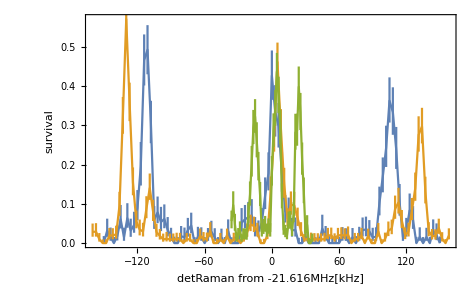

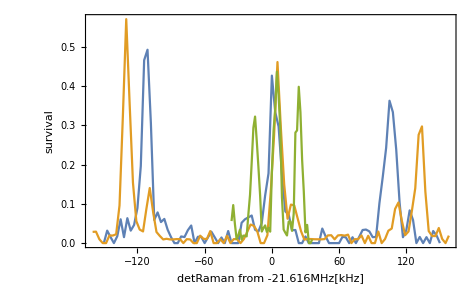

```mathematica
ErrorListPlot[{Rad1,Rad2,Ax},Joined->True,PlotRange->All,Axes->False,Frame->True,FrameLabel->{"detRaman from -21.616MHz[kHz]","survival"}]
ListPlot[{Rad1[[;;,1]],Rad2[[;;,1]],Ax[[;;,1]]},Joined->True,PlotRange->All,Axes->False,Frame->True,FrameLabel->{"detRaman from -21.616MHz[kHz]","survival"}]
```